In this notebook we will be calculating the dimensionless functions R_≫ and R_≪

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
sawSpecDictLL=Import["N-Specs/sawSpecsLL.m"];
boxSpecDictLL=Import["N-Specs/boxSpecsLL.m"];
sawSpecDictGG=Import["N-Specs/sawSpecsGG.m"];
boxSpecDictGG=Import["N-Specs/boxSpecsGG.m"];

(* In defining the sepctra we normalized the neutrino spectrum to integrate to 1, and scaled out  α d^2 Z^2 from the cross section *) 
ΦνSolar= 6.538802954197485*10^10;
dRef=1.97 10^-9(* MeV^-1 *) 197 (* MeV fm *) 10^-13(* fm per cm  *);
Zref=12;
overallNormalization= α ΦνSolar dRef^2 10^30/.α-> 1/137;
VnARef=10^30;
overallNormalization
```

0.718857

```mathematica
Γ=(d^2 mN^3)/(4π);
decEqRadEarth= Assuming[{mN>0,d>0},d/.Solve[197/Γ==6.4 10^3* 10^18 ,d]⟦2⟧//Quiet](* fm per km*)
```

(6.21939×10^-10)/mN^(3/2)

## Borexino Data

```mathematica
SetDirectory[NotebookDirectory[]];
fit7Be= Import["BorexinoData/bxno-fit-7be.csv"];
fitpep= Import["BorexinoData/bxno-fit-pep.csv"];
fit8B= Import["BorexinoData/bxno-fit-8b.csv"];
borexDat=Import["BorexinoData/Borexino.dat"];
numPhotons =Flatten@Take[Transpose[borexDat],{2,2}];
obsBins =Flatten@Take[Transpose[borexDat],{5,5}];
binWidths=Flatten@Take[Transpose[borexDat],{4,4}];
energies=Flatten@Take[Transpose[borexDat],{3,3}];
residuals=Flatten@Take[Transpose[borexDat],{7,7}];
errors=Flatten@Take[Transpose[borexDat],{6,6}];
fitBins=Flatten[Thread[Plus[Flatten@Thread[Times[-residuals,errors]],obsBins]]];
fitRate=Transpose[{0.001 energies,Flatten@Thread[Divide[fitBins,binWidths]]}];
obsRate=Transpose[{0.001 energies,Flatten@Thread[Divide[obsBins,binWidths]]}];
resRate=Transpose[{0.001 energies,Flatten@Thread[Divide[Flatten@Thread[Plus[fitBins,-obsBins]],binWidths]]}];

line1=Line[{{0,Log[0.1]},{0.8,Log[0.1]}}];
line2=Line[{{0.8,Log[0.01]},{2.5,Log[0.01]}}];


energyOfComparison=0.73;
be7tobkgRatio=(0.0815/0.1156);
currentRatio=(Interpolation@fit7Be)[energyOfComparison]/(Interpolation@obsRate)[energyOfComparison]
reScale=({#⟦1⟧,be7tobkgRatio/currentRatio#⟦2⟧}&);
LLplt1=ListLogPlot[{obsRate,fitRate,({#⟦1⟧,300#⟦2⟧}&)/@ sawSpecDictLL[(Keys@sawSpecDictLL)⟦22⟧],({#⟦1⟧,50#⟦2⟧}&)/@ sawSpecDictLL[(Keys@sawSpecDictLL)⟦12⟧],({#⟦1⟧,3000#⟦2⟧}&)/@ sawSpecDictLL[(Keys@sawSpecDictLL)⟦29⟧], reScale/@fit7Be,reScale/@fitpep,reScale/@ fit8B},PlotStyle-> {Automatic,Automatic,Dashed,Dotted,DotDashed,{Dashed,Thick,Blue},{Dashed,Thick,Blue},{Dashed,Thick,Blue}},Joined->True,PlotRange->{{0.2,2.5},{0.00005,110}},GridLines->{{{0.8,{Black,Thick}}},{}},PlotLegends->Placed[ {None,None,"m_N=1.08 MeV","m_N=115  keV","m_N=5.17 MeV"},{0.7,0.8}],Epilog->{{Directive[Thick],line1,line2},Inset[Framed[Style[Text["^8B "],12,Blue],Background->White,RoundingRadius->6,FrameMargins->1.25],{2.35,Log[1.8 10^-4]}] ,
Inset[Framed[Style[Text["^7Be"],12,Blue],Background->White,RoundingRadius->6,FrameMargins->1.25],{0.5,Log[0.03]}],
Inset[Framed[Style[Text["pep"],12,Blue],Background->White,RoundingRadius->6,FrameMargins->1.25],{1.4,Log[0.0003]}]  } ];
LLplt2=ListLogPlot[{resRate},Joined->False,PlotRange->{{0.2,2.5},Full},PlotStyle->Black];
```

2.76893

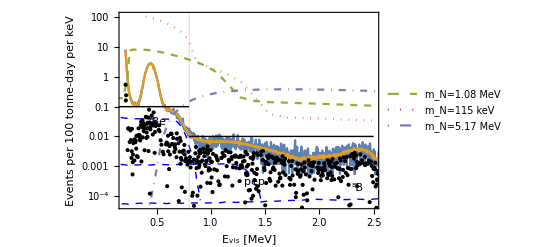

```mathematica
fig=Show[LLplt1,LLplt2,Frame-> True,FrameStyle-> Black,FrameLabel->(Style[#,12]&)/@{"E_vis  [MeV]","Events per 100 tonne-day per keV ","","Arbitrary Units"}]
```

```mathematica
Export["PDFs/BXNO-data.pdf",fig];
```

## Super Kamiokande Data

/Users/ryanplestid/Research/Physics_Projects/Archived_Projects/Solar-Upscatter-Dipole/Mathematica/PaperI-clean/BorexinoData

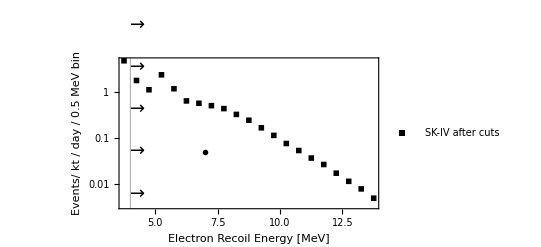

```mathematica
ListLogPlot[Import["SK-Data/SK-IV.csv"],PlotMarkers->Style["■", Black],PlotTheme->"Monochrome",Frame->True,FrameLabel->(Style[#,12]&)/@{"Electron Recoil Energy   [MeV]","Events/ kt / day / 0.5 MeV bin"},GridLines->{{4},{}},GridLinesStyle->Directive[Gray, Thick],Epilog->{Table[Inset[Style["→",18],Scaled[{0.07,0.1(1+2.8n)}]],{n,0,4}],Inset[Style["4.62 Events / kt / day",13],{7,-3}]},PlotLegends->Placed[{"SK-IV after cuts"},{0.6,0.85}]]
```